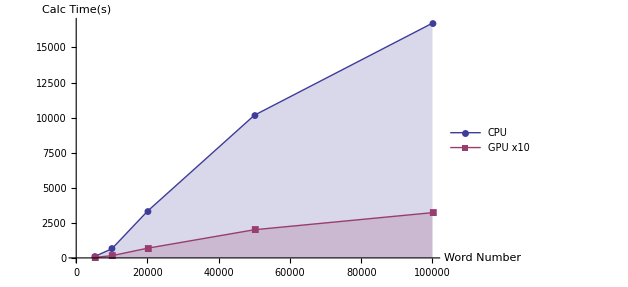

```mathematica
ListLinePlot[{{{5000,80.4},{10000,649.4},{20000,3327.9},{50000,10166.7},{100000,16731.3}},{{5000,3.1*10},{10000,15.8*10},{20000,69.0*10},{50000,200.7*10},{100000,322.6*10}}},Filling->Axis,PlotLegends->{"CPU","GPU x10"},AxesLabel->{"Word Number", "Calc Time(s)"},PlotLabel->"",Mesh->All,PlotMarkers->Automatic]
```

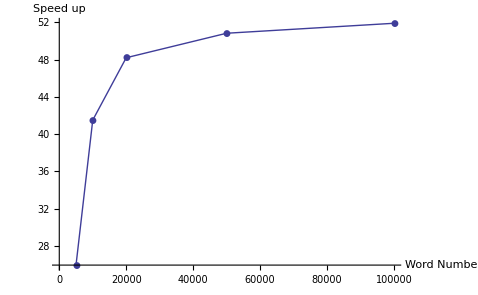

```mathematica
ListLinePlot[{{5000,25.93},{10000,41.5},{20000,48.2},{50000,50.83},{100000,51.9}},PlotLegends->"",AxesLabel->{"Word Number", "Speed up"},PlotLabel->"",Mesh->All,PlotMarkers->Automatic]
```

```mathematica
gpu32data={{32,32,8.133163},{32,64,5.349875},{32,96,4.598676},{32,128,4.128045},{32,160,3.887510},{32,192,3.636363},{32,224,3.547430},{32,256,3.430050},{32,288,3.326569},{32,320,3.275342},{64,32,5.424714},{64,64,4.076666},{64,96,3.604180},{64,128,3.410899},{64,160,3.248351},{64,192,3.230668},{64,224,3.227027},{64,256,3.193037},{64,288,3.232814},{64,320,3.248539},{96,32,4.417304},{96,64,3.558419},{96,96,3.281850},{96,128,3.088865},{96,160,3.085105},{96,192,3.111155},{96,224,3.225169},{96,256,3.330358},{96,288,3.429622},{96,320,3.686845},{128,32,4.102081},{128,64,3.359744},{128,96,3.224665},{128,128,3.159424},{128,160,3.276011},{128,192,3.334825},{128,224,3.713047},{128,256,3.727437},{128,288,4.084048},{128,320,4.152590},{160,32,3.802739},{160,64,3.256899},{160,96,3.110081},{160,128,3.193742},{160,160,3.497425},{160,192,3.713980},{160,224,4.089361},{160,256,4.043111},{160,288,4.521031},{160,320,4.296749},{192,32,3.460590},{192,64,3.207883},{192,96,3.157070},{192,128,3.329242},{192,160,3.609831},{192,192,3.971989},{192,224,4.163397},{192,256,4.429620},{192,288,4.446609},{192,320,4.047139},{224,32,3.535474},{224,64,3.156083},{224,96,3.348413},{224,128,3.653536},{224,160,4.118178},{224,192,4.265368},{224,224,4.540151},{224,256,4.292868},{224,288,4.244881},{224,320,3.917865},{256,32,3.415093},{256,64,3.104883},{256,96,3.405834},{256,128,3.689713},{256,160,4.327923},{256,192,4.352586},{256,224,4.368506},{256,256,4.083134},{256,288,4.126555},{256,320,4.033219},{288,32,3.241637},{288,64,3.140351},{288,96,3.526014},{288,128,3.904792},{288,160,4.320619},{288,192,4.180800},{288,224,4.209561},{288,256,4.082115},{288,288,4.183843},{288,320,4.168301},{320,32,3.285387},{320,64,3.172388},{320,96,3.833110},{320,128,4.176536},{320,160,4.307824},{320,192,3.977210},{320,224,4.113975},{320,256,4.121606},{320,288,4.331598},{320,320,4.201847}};
ListPlot3D[gpu32data,Mesh-> All,AxesLabel->{"Blocks","Threads", "Running Time"},ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
gpu32data10000={{32,32,63.296795},{32,64,33.333093},{32,96,26.805489},{32,128,23.516207},{32,160,21.325226},{32,192,19.905055},{32,224,18.851662},{32,256,17.821714},{32,288,17.688259},{32,320,17.478684},{64,32,40.065595},{64,64,22.407172},{64,96,18.881891},{64,128,16.803424},{64,160,17.234679},{64,192,16.763688},{64,224,16.582252},{64,256,15.791603},{64,288,17.437409},{64,320,17.926430},{96,32,26.924177},{96,64,19.542287},{96,96,17.063021},{96,128,16.327952},{96,160,16.465866},{96,192,17.257449},{96,224,17.952794},{96,256,19.515337},{96,288,21.197620},{96,320,22.901018},{128,32,23.514927},{128,64,17.874005},{128,96,17.180617},{128,128,15.798208},{128,160,19.163839},{128,192,20.284126},{128,224,23.393730},{128,256,23.861228},{128,288,27.412932},{128,320,27.919993},{160,32,21.002176},{160,64,17.182790},{160,96,16.839253},{160,128,17.848610},{160,160,21.587662},{160,192,23.930964},{160,224,27.267021},{160,256,27.097484},{160,288,30.287364},{160,320,28.928652},{192,32,19.545985},{192,64,16.369420},{192,96,16.711870},{192,128,19.817623},{192,160,22.710997},{192,192,25.629002},{192,224,28.004853},{192,256,30.195417},{192,288,29.656848},{192,320,26.164773},{224,32,18.923932},{224,64,16.262331},{224,96,20.019312},{224,128,22.498584},{224,160,27.467209},{224,192,29.442617},{224,224,31.496784},{224,256,28.573646},{224,288,27.986915},{224,320,26.016813},{256,32,17.934418},{256,64,16.809692},{256,96,20.934225},{256,128,24.306953},{256,160,28.661336},{256,192,28.969541},{256,224,29.229714},{256,256,26.464645},{256,288,26.821099},{256,320,26.180069},{288,32,17.570381},{288,64,16.800169},{288,96,21.853613},{288,128,25.788702},{288,160,29.149863},{288,192,27.309017},{288,224,27.846460},{288,256,26.308265},{288,288,27.661518},{288,320,28.301251},{320,32,16.920475},{320,64,17.885884},{320,96,24.885145},{320,128,28.185503},{320,160,28.174574},{320,192,26.043103},{320,224,26.770967},{320,256,26.411415},{320,288,29.034413},{320,320,27.156035}};
ListPlot3D[gpu32data,Mesh-> All,AxesLabel->{"Blocks","Threads", "Running Time"},ColorFunction->"Rainbow"]
```

```mathematica
-Graphics3D-
-Graphics3D-
```